```mathematica
ClearAll["Global`*"]
```

```mathematica
k=QuantityMagnitude["BoltzmannConstant","Joules"/"Kelvins"]/QuantityMagnitude["ElementaryCharge","Coulombs"]//N;
```

```mathematica
$Assumptions=β>0&&J∈Reals && h ∈Reals&& n∈PositiveIntegers;
```

```mathematica
λ1=ⅇ^(β J)Cosh[β h]+√(ⅇ^(2β J)Sinh[β h]^2+ⅇ^(-2β J));
λ2=ⅇ^(β J)Cosh[β h]-√(ⅇ^(2β J)Sinh[β h]^2+ⅇ^(-2β J));
```

```mathematica
Z=λ1^n+λ2^n;
-D[Z,β]//Simplify
```

-n (ⅇ^(J β) Cosh[h β]+√(ⅇ^(-2 J β)+ⅇ^(2 J β) Sinh[h β]^2))^(-1+n) (ⅇ^(J β) J Cosh[h β]+ⅇ^(J β) h Sinh[h β]+(ⅇ^(-2 J β) (ⅇ^(4 J β) h Cosh[h β] Sinh[h β]+J (-1+ⅇ^(4 J β) Sinh[h β]^2)))/(√(ⅇ^(-2 J β)+ⅇ^(2 J β) Sinh[h β]^2)))-n (ⅇ^(J β) Cosh[h β]-√(ⅇ^(-2 J β)+ⅇ^(2 J β) Sinh[h β]^2))^(-1+n) (ⅇ^(J β) J Cosh[h β]+ⅇ^(J β) h Sinh[h β]+(ⅇ^(-2 J β) (J-ⅇ^(4 J β) J Sinh[h β]^2-1/2 ⅇ^(4 J β) h Sinh[2 h β]))/(√(ⅇ^(-2 J β)+ⅇ^(2 J β) Sinh[h β]^2)))

```mathematica
eigval[β_,J_,h_,s_]:=ⅇ^(β J)Cosh[β h]+s √(ⅇ^(2β J)Sinh[β h]^2+ⅇ^(-2β J));
LNZ[β_,J_,h_,n_Integer]:=Log[eigval[β,J,h,1]^n+eigval[β,J,h,-1]^n];
```

```mathematica
Energy[T_,J_,h_,n_Integer]:=-D[LNZ[β,J,h,n],β]/.β->1/T;
MagMoment[T_,J_,h_,n_Integer]:=T/n D[LNZ[1/T,J,hx,n],hx]/.hx->h;
Suscep[T_,J_,h_,n_Integer]:=D[MagMoment[T,J,hx,n],hx]/.hx->h
```

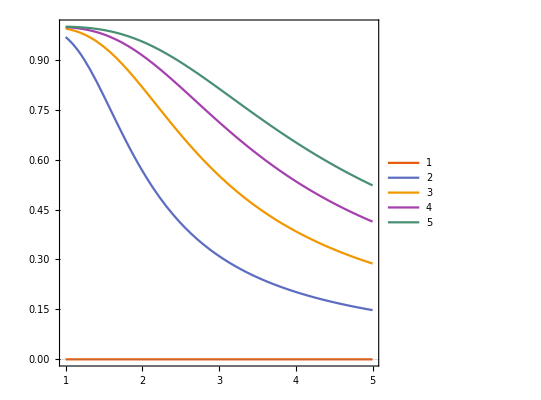

```mathematica
Plot[Evaluate@Table[MagMoment[T,1.,0.5t,100],{t,0,4}],{T,1.,5.},PlotTheme->"Scientific",PlotLegends->Automatic,AspectRatio->1.]
```